```mathematica
SetDirectory@NotebookDirectory[];
Import["QLanczos_package.m"];
```

## Parameters

```mathematica
th=10;(*multiple of noise*)
d=5;
Id=IdentityMatrix[d];
κ=0.1;
η=10.^-15;(*machine precision*)
```

```mathematica
MList=Table[10.^j,{j,4,20,1}];(*the measurement number for a real matrx element is M*)
rep=100;(*replications*)
```

## Model

```mathematica
Ham=HeisenbergHam;
```

## Spectrum

```mathematica
{Λ,U}=funSpectrum[Ham];
HamNorm=Max[Abs[Λ]]
Λ=Λ/HamNorm;
Eg=Λ[[1]]
```

17.0321

-1.

```mathematica
htot=27./HamNorm
```

1.58524

## Reference state

```mathematica
φ=φHeisenberg;
φ=Flatten[Conjugate[U].φ];
probφ=Abs[φ]^2;
```

```mathematica
pg=probφ[[1]](*pg>10^-3*)
ER=Total[probφ*Λ];
ϵR=ER-Eg
```

0.682614

0.119312

## Power

```mathematica
E0=Eg+1.;
{Hmat,Smat}=funMatP[Λ,E0,d,probφ];
```

```mathematica
EB=Hmat[[d,d]]/Smat[[d,d]];
ϵB=EB-Eg(*used to identify τ for GP, ITE and F*)
```

0.0072981

```mathematica
{EK,cn}=funSubDiag[Hmat+η*Id,Smat+η*Id];
ϵK=EK-Eg(*10^-9<ϵK<10^-2*)
```

0.000390209

```mathematica
costH=1.;
costS=1.;
ϵPList=funThrPracGP[MList,rep,Hmat,Smat,d,costH,costS,th,Eg];
```

## Chebyshev Polynomial

```mathematica
E0=0.;
{Hmat,Smat}=funMatCP[Λ,E0,d,probφ,htot];
```

```mathematica
costH=1.;
costS=1.;
ϵCPList=funThrPracF[MList,rep,Hmat,Smat,d,costH,costS,th,Eg];
```

## Gaussian-Power

```mathematica
τMIN=0;
τMAX=64;
While[True,
τ=(τMIN+τMAX)/2.;
{Hmat,Smat}=funMatGP[Λ,Eg,τ,1,probφ,htot];
EK=Hmat[[1,1]]/Smat[[1,1]];
err=EK-Eg;
If[err>ϵB,τMIN=τ];
If[err<ϵB,τMAX=τ];
(*Print[{err,τMIN,τMAX}];*)
If[Abs[err-ϵB]<10^-10,Break[]];
];
τ
```

6.34638

```mathematica
E0=Eg;
{Hmat,Smat}=funMatGP[Λ,E0,τ,d,probφ,htot];
```

```mathematica
costH=htot;
costS=1.;
ϵGPList=funThrPracF[MList,rep,Hmat,Smat,d,costH,costS,th,Eg];(*rescaled*)
```

## Inverse Power

```mathematica
E0=Eg-1.;
{Hmat,Smat}=funMatIP[Λ,E0,d,probφ];
```

```mathematica
costH=1.;
costS=1.;
ϵIPList=funThrPracGP[MList,rep,Hmat,Smat,d,costH,costS,th,Eg];
```

## Imaginary-time evolution

```mathematica
τMIN=0;
τMAX=64;
While[True,
τ=(τMIN+τMAX)/2.;
{Hmat,Smat}=funMatITE[Λ,Eg,τ,d,probφ];
EK=Hmat[[d,d]]/Smat[[d,d]];
err=EK-Eg;
If[err>ϵB,τMIN=τ];
If[err<ϵB,τMAX=τ];
(*Print[{err,τMIN,τMAX}];*)
If[Abs[err-ϵB]<10^-10,Break[]];
];
τ
```

1.1768

```mathematica
E0=Eg;
{Hmat,Smat}=funMatITE[Λ,E0,τ,d,probφ];
```

```mathematica
costH=1.;
costS=1.;
ϵITEList=funThrPracGP[MList,rep,Hmat,Smat,d,costH,costS,th,Eg];
```

## Real-time evolution

0.251327

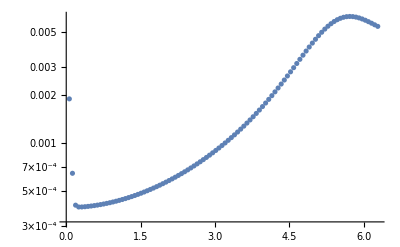

```mathematica
ΔtList=Table[(2.*π)/100 j,{j,1,100}];
ϵKList=ConstantArray[0,Length[ΔtList]];
Do[
Δt=ΔtList[[j]];
{Hmat,Smat}=funMatRTE[Λ,Eg,Δt,d,probφ];
{EK,cn}=funSubDiag[Hmat+η*Id,Smat+η*Id];
err=EK-Eg;
ϵKList[[j]]=err;
,{j,1,Length[ΔtList]}]
Δt=ΔtList[[Position[ϵKList,Min[ϵKList]][[1,1]]]]
ListLogPlot[Transpose[{ΔtList,ϵKList}],PlotRange->Full]
```

```mathematica
E0=Eg;
{Hmat,Smat}=funMatRTE[Λ,E0,Δt,d,probφ];
```

```mathematica
costH=1.;
costS=1.;
ϵRTEList=funThrPracRTE[MList,rep,Hmat,Smat,d,costH,costS,th,Eg];
```

## Filter

```mathematica
τMIN=0;
τMAX=64;
While[True,
τ=(τMIN+τMAX)/2.;
{Hmat,Smat}=funMatF[Λ,Eg,0,τ,1,probφ];
EK=Hmat[[1,1]]/Smat[[1,1]];
err=EK-Eg;
If[err>ϵB,τMIN=τ];
If[err<ϵB,τMAX=τ];
(*Print[{err,τMIN,τMAX}];*)
If[Abs[err-ϵB]<10^-10,Break[]];
];
τ
```

11.2447

0.02

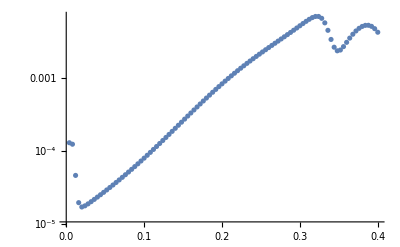

```mathematica
ΔEList=Table[2./(d*100)*j,{j,1,100}];
ϵKList=ConstantArray[0,Length[ΔEList]];
Do[(
ΔE=ΔEList[[j]];
{Hmat,Smat}=funMatF[Λ,Eg,ΔE,τ,d,probφ];
{EK,cn}=funSubDiag[Hmat+η*Id,Smat+η*Id];
err=EK-Eg;
ϵKList[[j]]=err;
),{j,1,Length[ΔEList]}]
ΔE=ΔEList[[Position[ϵKList,Min[ϵKList]][[1,1]]]]
ListLogPlot[Transpose[{ΔEList,ϵKList}],PlotRange->Full]
```

```mathematica
E0=Eg;
{Hmat,Smat}=funMatF[Λ,E0,ΔE,τ,d,probφ];
```

```mathematica
costH=1.;
costS=1.;
ϵFList=funThrPracF[MList,rep,Hmat,Smat,d,costH,costS,th,Eg];
```

## Plot

```mathematica
ϵPListκ=funExtract[ϵPList,MList,rep,κ];
ϵCPListκ=funExtract[ϵCPList,MList,rep,κ];
ϵGPListκ=funExtract[ϵGPList,MList,rep,κ];
ϵIPListκ=funExtract[ϵIPList,MList,rep,κ];
ϵITEListκ=funExtract[ϵITEList,MList,rep,κ];
ϵRTEListκ=funExtract[ϵRTEList,MList,rep,κ];
ϵFListκ=funExtract[ϵFList,MList,rep,κ];
```

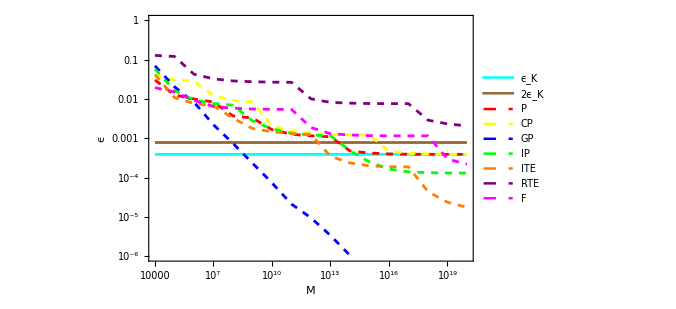

```mathematica
PR={{10^4,10^20},{10^-6,10^0}};
Fig1=ListLogLogPlot[{Transpose[{MList,0.*MList+1.*ϵK}],Transpose[{MList,0.*MList+2.*ϵK}],Transpose[{MList,ϵPListκ}],Transpose[{MList,ϵCPListκ}],Transpose[{MList,ϵGPListκ}],Transpose[{MList,ϵIPListκ}],Transpose[{MList,ϵITEListκ}],Transpose[{MList,ϵRTEListκ}],Transpose[{MList,ϵFListκ}]},PlotRange->PR,Joined->True,PlotStyle->{{Thickness[0.004],Cyan},{Thickness[0.004],Brown},{Thickness[0.004],Red,Dashed},{Thickness[0.004],Yellow,Dashed},{Thickness[0.004],Blue,Dashed},{Thickness[0.004],Green,Dashed},{Thickness[0.004],Orange,Dashed},{Thickness[0.004],Purple,Dashed},{Thickness[0.004],Magenta,Dashed}},Frame->True,FrameStyle->Directive[Black,Thickness[0.002]],FrameTicksStyle->Directive[Black,Thickness[0.002]],FrameLabel->{"M","ϵ"},LabelStyle->{FontSize->18,FontFamily->"Arial"},ImageSize->500,PlotLegends->Placed[LineLegend[{"ϵ_K","2ϵ_K","P","CP","GP","IP","ITE","RTE","F"},LegendFunction->(Framed[#,FrameStyle->LightGray]&),LegendMarkerSize->{16,8},LabelStyle->{Black,Bold,FontSize->12,FontFamily->"Arial"},LegendMargins->0,LegendLayout->{"Column",3}],{0.79,0.84}]]
```

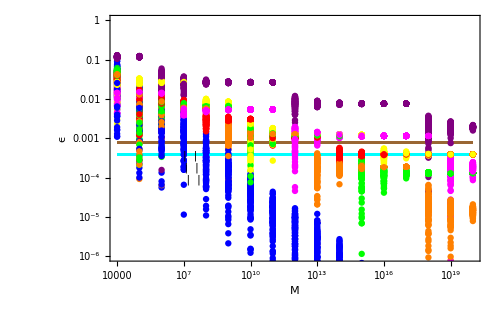

```mathematica
lleg1=LineLegend[{Cyan},{"ϵ_K"},LegendMarkerSize->{14,7},LabelStyle->{Black,Bold,FontSize->12,FontFamily->"Arial"},LegendMargins->0];
lleg2=LineLegend[{Brown},{"2ϵ_K"},LegendMarkerSize->{14,7},LabelStyle->{Black,Bold,FontSize->12,FontFamily->"Arial"},LegendMargins->0];
pleg1=PointLegend[{Red},{"P"},LegendMarkerSize->{14,7},LabelStyle->{Black,Bold,FontSize->12,FontFamily->"Arial"},LegendMargins->0];
pleg2=PointLegend[{Yellow},{"CP"},LegendMarkerSize->{14,7},LabelStyle->{Black,Bold,FontSize->12,FontFamily->"Arial"},LegendMargins->0];
pleg3=PointLegend[{Blue},{"GP"},LegendMarkerSize->{14,7},LabelStyle->{Black,Bold,FontSize->12,FontFamily->"Arial"},LegendMargins->0];
pleg4=PointLegend[{Green},{"IP"},LegendMarkerSize->{14,7},LabelStyle->{Black,Bold,FontSize->12,FontFamily->"Arial"},LegendMargins->0];
pleg5=PointLegend[{Orange},{"ITE"},LegendMarkerSize->{14,7},LabelStyle->{Black,Bold,FontSize->12,FontFamily->"Arial"},LegendMargins->0];
pleg6=PointLegend[{Purple},{"RTE"},LegendMarkerSize->{14,7},LabelStyle->{Black,Bold,FontSize->12,FontFamily->"Arial"},LegendMargins->0];
pleg7=PointLegend[{Magenta},{"F"},LegendMarkerSize->{14,7},LabelStyle->{Black,Bold,FontSize->12,FontFamily->"Arial"},LegendMargins->0];
Fig2=
Legended[Show[Table[ListLogLogPlot[{Transpose[{MList,0.*MList+1.*ϵK}],Transpose[{MList,0.*MList+2.*ϵK}],Transpose[{MList,ϵPList[[i]]}],Transpose[{MList,ϵCPList[[i]]}],Transpose[{MList,ϵGPList[[i]]}],Transpose[{MList,ϵIPList[[i]]}],Transpose[{MList,ϵITEList[[i]]}],Transpose[{MList,ϵRTEList[[i]]}],Transpose[{MList,ϵFList[[i]]}]},PlotRange->PR,Joined->{True,True,False,False,False,False,False,False,False},Frame->True,FrameStyle->Directive[Black,Thickness[0.002]],FrameTicksStyle->Directive[Black,Thickness[0.002],18],FrameLabel->{"M","ϵ"},LabelStyle->{FontSize->22,FontFamily->"Arial"},ImageSize->500,PlotStyle->{Cyan,Brown,Red,Yellow,Blue,Green,Orange,Purple,Magenta}],{i,1,rep}]],Placed[Grid[{{lleg1,pleg2,pleg5},{lleg2,pleg3,pleg6},{pleg1,pleg4,pleg7}},Alignment->Left,Frame->True,FrameStyle->LightGray],{{0.22,0.45},{0.5,1.5}}]]
```

```mathematica
Export["C:\\Users\\John\\Desktop\\Revise\\Thresholding comparison th=10.pdf",Fig1];
```